Analysis of transition frequencies for △p=0 with △m = -1,0,1 and different initial and final m scenarios

Filenames for △m=-1,0,1 with transitions of the form △p=0

```mathematica
Scenario1="C:\\University\\Honours\\Formal delta m experiments\\Scenario 1.txt";
```

```mathematica
Scenario3="C:\\University\\Honours\\Formal delta m experiments\\Scenario 3.txt";
```

```mathematica
Scenario5="C:\\University\\Honours\\Formal delta m experiments\\scenario 5.txt";
```

```mathematica
Scenario7 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 7.txt";
```

```mathematica
Scenario10 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 10.txt";
```

```mathematica
Scenario11 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 11.txt";
```

```mathematica
Scenario12 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 12.txt";
```

```mathematica
datalist=ReadList[Scenario1];
```

Functions ReadFile, ReadFileB reads Transition frequencies as a function of principle quantum number <n>

```mathematica
ReadFile[min_, max_,opt_:1]:=(nvals=Range[min, max, 5]; lists=Map[ReadFileB ,nvals];
Return[lists])
```

```mathematica
ReadFileB[nval_]:=(posn=Position[datalist, {nval,_,_,_,_,_,_}];e=Extract[datalist, posn]; Return[GetLastLog10@@@e])
```

Function GetLast* & GetLog* operate on lists to extract the data

```mathematica
GetLast[_,_,_,_,_,_,last_]:=last
```

```mathematica
GetLastLog10[_,_,_,_,_,_,last_]:=Log10[last]
```

```mathematica
GetPLast[in_,il_,_,_,_,_, last_]:={(in-il),last }
```

```mathematica
GetPLog10[in_,il_,_,_,_,_, last_]:={(in-il),Log[last] }
```

Scenario 1: △m = 0, △l = +1, △p = -2, mi = mf = 0

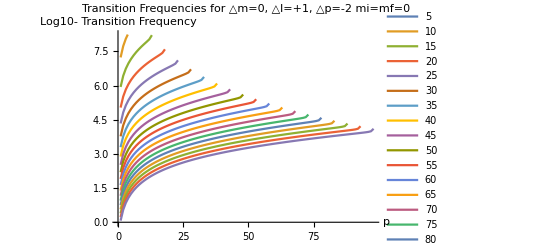

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=0, △l=+1, △p=-2 mi=mf=0"]
```

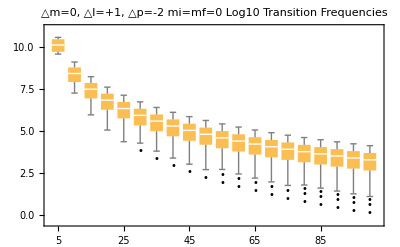

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=0, △l=+1, △p=-2 mi=mf=0\nLog10 Transition Frequencies"]
```

```mathematica
list=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data=Table[Flatten[Last/@Cases[list, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means=Mean/@data;
```

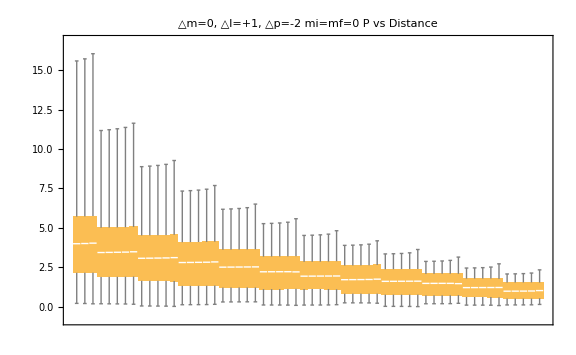

```mathematica
BoxWhiskerChart[Sqrt[Power[data-means, 2]],PlotLabel->"△m=0, △l=+1, △p=-2 mi=mf=0\nP vs Distance"]
```

Scenario 3: △m = +1, △l = +1, △p = -2, mi = 0 mf = +1

```mathematica
datalist=ReadList[Scenario3];
```

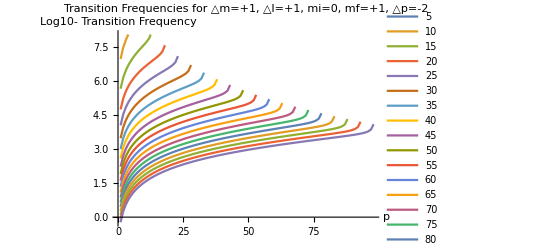

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=+1, △l=+1, mi=0, mf=+1, △p=-2"]
```

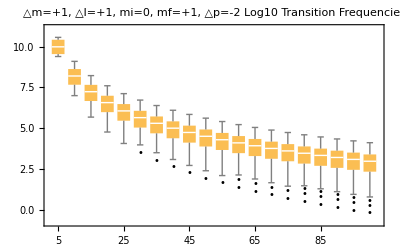

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=+1, △l=+1, mi=0, mf=+1, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

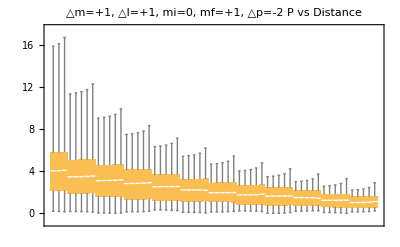

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=+1, △l=+1, mi=0, mf=+1, △p=-2\nP vs Distance"]
```

Scenario 5: △m=+1 with mi = li and mf = lf, △l=+1, △p = -2

```mathematica
datalist=ReadList[Scenario5];
```

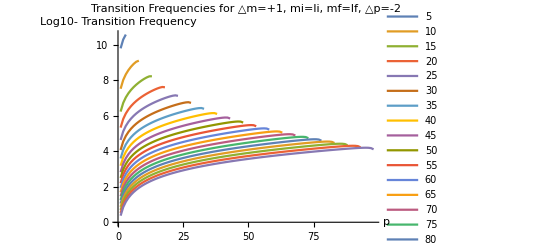

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=+1, mi=li, mf=lf, △p=-2"]
```

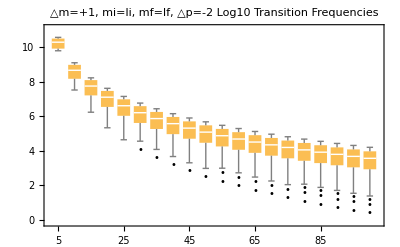

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=+1, mi=li, mf=lf, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list3=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data3=Table[Flatten[Last/@Cases[list3, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means3=Mean/@data3;
```

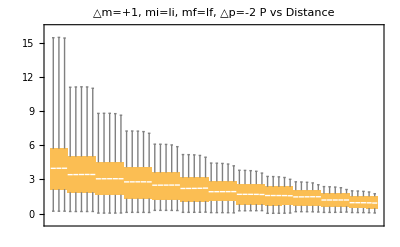

```mathematica
BoxWhiskerChart[Sqrt[Power[data3-means3, 2]],PlotLabel->"△m=+1, mi=li, mf=lf, △p=-2\nP vs Distance"]
```

```mathematica
Scenario 7: △m=-1 with mi = -li and mf = -lf, △l=+1, △p = -2
```

Syntax::sntxf: "Scenario 8" cannot be followed by 
    ": △m=+1 with mi = -li and mf = -lf, △l=-1,
      △p = 0".

Syntax::sntxf: " △m=+1 with mi = -li a" cannot be followed by 
    "nd mf = -lf, △l=-1, △p = 0".

Syntax::sntxf: "" cannot be followed by 
    "iangle]m=+1 with mi = -li and mf = -lf, △l=-1,
      △p = 0".

0

```mathematica
datalist=ReadList[Scenario7];
```

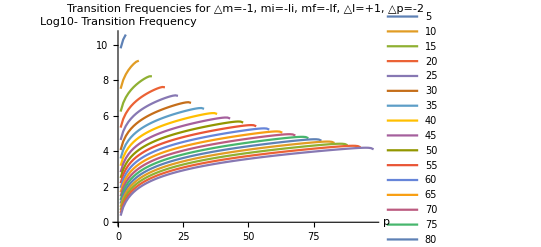

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=-1, mi=-li, mf=-lf, △l=+1, △p=-2"]
```

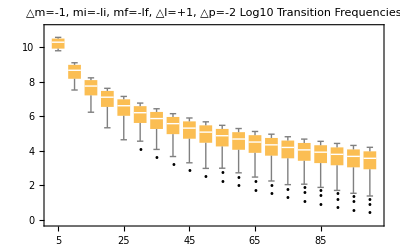

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=-1, mi=-li, mf=-lf, △l=+1, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list3=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data3=Table[Flatten[Last/@Cases[list3, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means3=Mean/@data3;
```

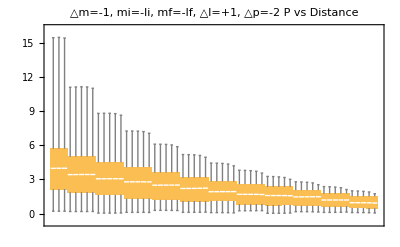

```mathematica
BoxWhiskerChart[Sqrt[Power[data3-means3, 2]],PlotLabel->"△m=-1, mi=-li, mf=-lf, △l=+1, △p=-2\nP vs Distance"]
```

Scenario 10: △m=0 with mi = mf = ni-5, △l=+1, △p = -2

```mathematica
datalist=ReadList[Scenario10];
```

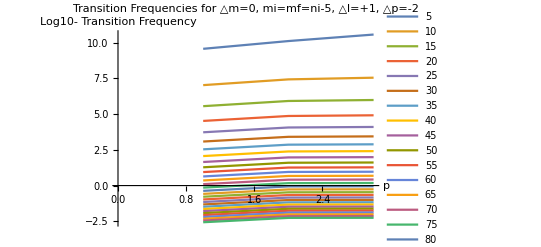

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=0, mi=mf=ni-5, △l=+1, △p=-2"]
```

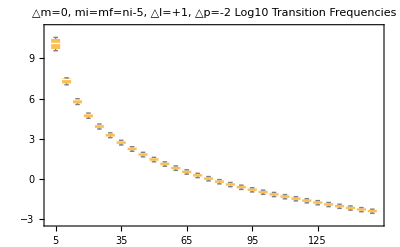

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=0, mi=mf=ni-5, △l=+1, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

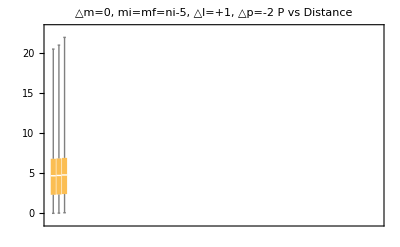

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=0, mi=mf=ni-5, △l=+1, △p=-2\nP vs Distance"]
```

Scenario 11: △m=-1 with mi = ni-5, mf = ni-6, △l=+1, △p = -2

```mathematica
datalist=ReadList[Scenario11];
```

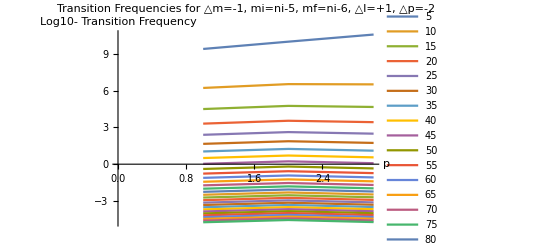

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=-1, mi=ni-5, mf=ni-6, △l=+1, △p=-2"]
```

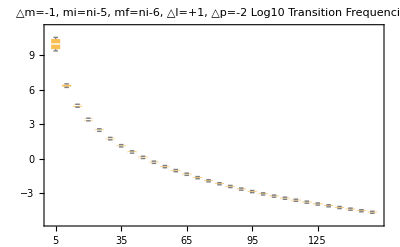

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=-1, mi=ni-5, mf=ni-6, △l=+1, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

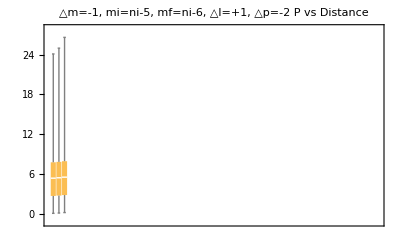

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=-1, mi=ni-5, mf=ni-6, △l=+1, △p=-2\nP vs Distance"]
```

Scenario 12: △m=+1 with mi = ni-5, mf = ni-4, △l=+1, △p = -2

```mathematica
datalist=ReadList[Scenario12];
```

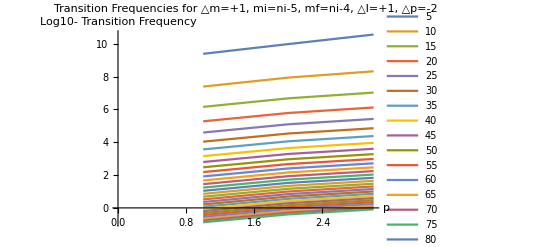

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=+1, mi=ni-5, mf=ni-4, △l=+1, △p=-2"]
```

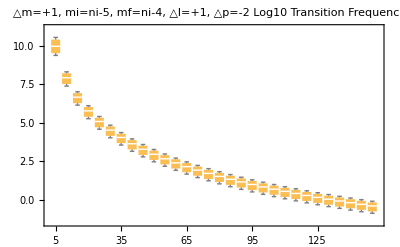

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=+1, mi=ni-5, mf=ni-4, △l=+1, △p=-2\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

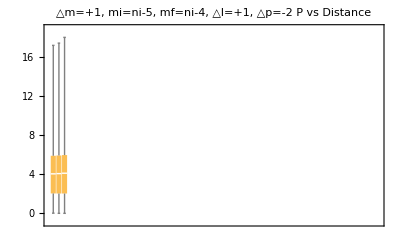

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=+1, mi=ni-5, mf=ni-4, △l=+1, △p=-2\nP vs Distance"]
```